1/15 (5+6 f^2-2 f^3+6 f^4)

1/2 Ene (1+1/15 (-5-(6 F^2)/Ene^2+(2 F^3)/Ene^3-(6 F^4)/Ene^4))+(F^2 (-1+1/5 (5+(6 F^2)/Ene^2-(2 F^3)/Ene^3+(6 F^4)/Ene^4)))/(2 Ene)

1/2 Ene (1+1/15 (-5-(6 F^2)/Ene^2+(2 F^3)/Ene^3-(6 F^4)/Ene^4))+1/2 Ene (-1+1/5 (5+(6 F^2)/Ene^2-(2 F^3)/Ene^3+(6 F^4)/Ene^4))

(2 F (2 Ene^2-Ene F+4 F^2))/(5 Ene^3)

(5 Ene^4-6 Ene^2 F^2+4 Ene F^3-18 F^4)/(15 Ene^4)

1/15 (6 f-3 f^2+12 f^3+√3 √((-1+f)^2 (25+50 f+57 f^2+72 f^3+48 f^4)))

1/15 (6 f-3 f^2+12 f^3-√3 √((-1+f)^2 (25+50 f+57 f^2+72 f^3+48 f^4)))

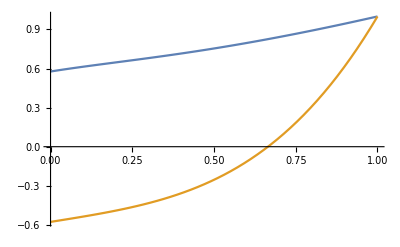

```mathematica
ChiEdd[f_]=(5+6*f^2-2*f^3+6f^4)/15
Press1[Ene_,F_]=(1-ChiEdd[F/Ene])/2*Ene+(3*ChiEdd[F/Ene]-1)/2*F*F/Ene
Press[Ene_,F_]=(1-ChiEdd[F/Ene])/2*Ene+(3*ChiEdd[F/Ene]-1)/2*Ene
Bterm[Ene_,F_]=Simplify[D[Press[Ene,F],F]]
Cterm[Ene_,F_]=Simplify[D[Press[Ene,F],Ene]]
Charp[f_]=Simplify[(Bterm[1,f]+Sqrt[Bterm[1,f]*Bterm[1,f]+4*Cterm[1,f]])/2]
Charm[f_]=Simplify[(Bterm[1,f]-Sqrt[Bterm[1,f]*Bterm[1,f]+4*Cterm[1,f]])/2]
Plot[{Charp[f],Charm[f]},{f,0,1}]
```

1/15 (5+6 f^2+2 f^3+6 f^4)

1/2 Ene (1+1/15 (-5-(6 F^2)/Ene^2-(2 F^3)/Ene^3-(6 F^4)/Ene^4))+(F^2 (-1+1/5 (5+(6 F^2)/Ene^2+(2 F^3)/Ene^3+(6 F^4)/Ene^4)))/(2 Ene)

1/2 Ene (1+1/15 (-5-(6 F^2)/Ene^2-(2 F^3)/Ene^3-(6 F^4)/Ene^4))+1/2 Ene (-1+1/5 (5+(6 F^2)/Ene^2+(2 F^3)/Ene^3+(6 F^4)/Ene^4))

(2 F (2 Ene^2+Ene F+4 F^2))/(5 Ene^3)

-(-5 Ene^4+6 Ene^2 F^2+4 Ene F^3+18 F^4)/(15 Ene^4)

1/15 (6 f+3 f^2+12 f^3+√3 √((1+f)^2 (25-50 f+57 f^2-72 f^3+48 f^4)))

1/15 (6 f+3 f^2+12 f^3-√3 √((1+f)^2 (25-50 f+57 f^2-72 f^3+48 f^4)))

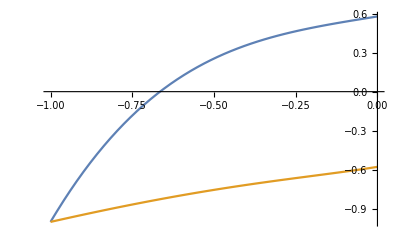

```mathematica
ChiEdd[f_]=(5+6*f^2+2*f^3+6 f^4)/15
Press1[Ene_,F_]=(1-ChiEdd[F/Ene])/2*Ene+(3*ChiEdd[F/Ene]-1)/2*F*F/Ene
Press[Ene_,F_]=(1-ChiEdd[F/Ene])/2*Ene+(3*ChiEdd[F/Ene]-1)/2*Ene
Bterm[Ene_,F_]=Simplify[D[Press[Ene,F],F]]
Cterm[Ene_,F_]=Simplify[D[Press[Ene,F],Ene]]
Charp[f_]=Simplify[(Bterm[1,f]+Sqrt[Bterm[1,f]*Bterm[1,f]+4*Cterm[1,f]])/2]
Charm[f_]=Simplify[(Bterm[1,f]-Sqrt[Bterm[1,f]*Bterm[1,f]+4*Cterm[1,f]])/2]
Plot[{Charp[f],Charm[f]},{f,-1,0}]
```

```mathematica
PressN1[Ene_,F_,Fp_]=(1-ChiEdd[Sqrt[F*F+Fp*Fp]/Ene])/2*Ene + (3*ChiEdd[Sqrt[F*F+Fp*Fp]/Ene]-1)/2*Ene*F*F/(F*F+Fp*Fp)
```

1/2 Ene (1+1/15 (-5-(6 (F^2+Fp^2))/Ene^2+(2 (F^2+Fp^2)^(3/2))/Ene^3-(6 (F^2+Fp^2)^2)/Ene^4))+(Ene F^2 (-1+1/5 (5+(6 (F^2+Fp^2))/Ene^2-(2 (F^2+Fp^2)^(3/2))/Ene^3+(6 (F^2+Fp^2)^2)/Ene^4)))/(2 (F^2+Fp^2))

```mathematica
BtermN[Ene_,F_,Fp_]=D[PressN[Ene,F,Fp],F]
CtermN[Ene_,F_,Fp_]=D[PressN[Ene,F,Fp],Ene]
```

PressN^(0,1,0)[Ene,F,Fp]

PressN^(1,0,0)[Ene,F,Fp]

```mathematica
CharNpn[f_]=(BtermN[1,f,0]+Sqrt[BtermN[1,f,0]*BtermN[1,f,0] +4*CtermN[1,f,0]])/2
CharNmn[f_]=(BtermN[1,f,0]-Sqrt[BtermN[1,f,0]*BtermN[1,f,0] +4*CtermN[1,f,0]])/2
```

1/2 (PressN^(0,1,0)[1,f,0]+√((PressN^(0,1,0)[1,f,0])^2+4 PressN^(1,0,0)[1,f,0]))

1/2 (PressN^(0,1,0)[1,f,0]-√((PressN^(0,1,0)[1,f,0])^2+4 PressN^(1,0,0)[1,f,0]))

```mathematica
Plot[ {CharNpn[f] ,CharNmn[f]}, {f,-1,1} ]
```

-Graphics-

```mathematica
CharNpp[f_]=(BtermN[1,0,f]+Sqrt[BtermN[1,0,f]*BtermN[1,0,f] +4*CtermN[1,0,f]])/2
CharNmp[f_]=(BtermN[1,0,f]-Sqrt[BtermN[1,0,f]*BtermN[1,0,f] +4*CtermN[1,0,f]])/2
```

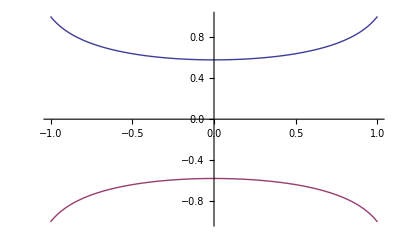

```mathematica
Plot[ {CharNpp[f] ,CharNmp[f]}, {f,-1,1} ]
```

```mathematica
CharNpT[f_,theta_]=(BtermN[1,f*Cos[theta],f*Sin[theta]]+Sqrt[BtermN[1,f*Cos[theta],f*Sin[theta]]*BtermN[1,f*Cos[theta],f*Sin[theta]] +4*CtermN[1,f*Cos[theta],f*Sin[theta]] ])/2
CharNmT[f_,theta_]=(BtermN[1,f*Cos[theta],f*Sin[theta]]-Sqrt[BtermN[1,f*Cos[theta],f*Sin[theta]]*BtermN[1,f*Cos[theta],f*Sin[theta]] +4*CtermN[1,f*Cos[theta],f*Sin[theta]] ])/2
```

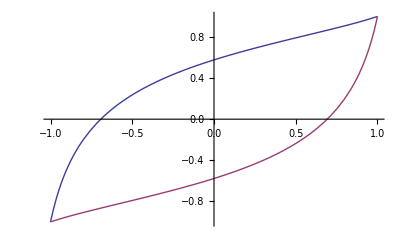

```mathematica
Plot[ {CharNpT[f,0] ,CharNmT[f,0]}, {f,-1,1} ]
```

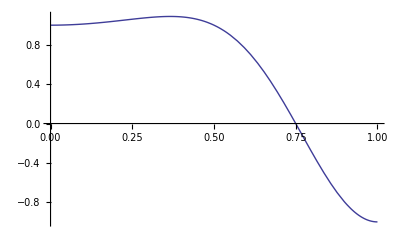

```mathematica
Plot[ CharNpT[1,Pi*theta] , {theta,0,1} ]
```